# Spiral Attractor

### Non - Compact x - z Phase Space

```mathematica
(*Define the parameters for this case*)
wx=-1.5;
q=0.1;
ϵ=0.01;
```

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
dex:=x'=-3*x*(1+wx+ϵ*x)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{dex==0,dez==0},{x,z}]
```

{{x→3/q,z→-(3 (q+q wx+3 ϵ))/q^2},{x→0,z→0},{x→-(1+wx)/ϵ,z→0}}

```mathematica
FP[1]={x/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],z/.FPs[[2,2]]};
FP[3]={x/.FPs[[3,1]],z/.FPs[[3,2]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[dex,x],D[dex,z]}, {D[dez,x],D[dez,z]}}];
J//MatrixForm
```

(-1.5+1.5 x-1. z | -x
z | -3+x)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(2.
0.) | (1.5 | -2.
0. | -1.) | (1.5
-1.) | (1. | 0.
0.624695 | 0.780869)
(3.
0.75) | (2.25 | -3.
0.75 | 0.) | (1.125+0.992157 ⅈ
1.125-0.992157 ⅈ) | (0.894427+0. ⅈ | 0.33541-0.295804 ⅈ
0.894427+0. ⅈ | 0.33541+0.295804 ⅈ)
(0.
0.) | (-1.5 | 0.
0. | -3.) | (-3.
-1.5) | (0. | 1.
-1. | 0.)

```mathematica
(*Find condition for first fixed point to be complex*)
wxCond=Solve[4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2==0,{q,ϵ,wx}]
```

Solve::ivar: 1 is not a valid variable.

Solve[False,{1,-0.25,-0.5}]

```mathematica
wxCondition=wx/.wxCond[[1]]
```

ReplaceAll::reps: {False} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-0.5/.False

```mathematica
(*Maximum value wx can be for the first fixed point to be complex for positive q and negative ϵ -> Fig. 9b*)
(*For this wx the two eigenvalues are the same*)
wxMax=wxCondition/.{ϵ->0.01,q->0.1}
```

-0.5/.False

```mathematica
(*Define the differential equations in terms of their variables*)
DE[wx_,q_,ϵ_]=dex;
DM[q_]=dez;
```

```mathematica
StreamPlot[{DE[wx,q,ϵ],DM[q]},{x,0,5},{z,0,3},FrameLabel->{"x","z"}]
```

### Non-Compact x - y - z Phase Space

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
de1:=x'=-3*y*x*(1+wx+ϵ*x)-q*x*y*z
de2:=y'=-y^2-(1/6)*(x+z+3*wx*x+3*ϵ*x^2)
de3:=z'=-3*y*z + q*x*y*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0},{x,y,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0,z→-x-3 wx x-3 x^2 ϵ},{x→0,y→0,z→0},{x→3/q,y→-(√(-q wx-3 ϵ))/q,z→-(3 (q+q wx+3 ϵ))/q^2},{x→3/q,y→(√(-q wx-3 ϵ))/q,z→-(3 (q+q wx+3 ϵ))/q^2},{x→(-1-wx)/ϵ,y→-(√(-1-wx))/(√3 √ϵ),z→0},{x→(-1-wx)/ϵ,y→(√(-1-wx))/(√3 √ϵ),z→0}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x,y/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],y/.FPs[[2,2]],z/.FPs[[2,3]]};
FP[3]={x/.FPs[[3,1]],y/.FPs[[3,2]],z/.FPs[[3,3]]};
FP[4]={x/.FPs[[4,1]],y/.FPs[[4,2]],z/.FPs[[4,3]]};
FP[5]={x/.FPs[[5,1]],y/.FPs[[5,2]],z/.FPs[[5,3]]};
FP[6]={x/.FPs[[6,1]],y/.FPs[[6,2]],z/.FPs[[6,3]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,6}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,y],D[de1,z]}, {D[de2,x],D[de2,y],D[de2,z]},{D[de3,x],D[de3,y],D[de3,z]}}];
J//MatrixForm
```

(y (-1.5+1.5 x-1. z) | x (-1.5+0.75 x-z) | -x y
0.0833333+0.25 x | -2 y | -1/6
y z | (-3+x) z | (-3+x) y)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm},{i,1,6}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0
0.5 x+0.75 x^2) | (0 | x (-1.5+0.25 x-0.75 x^2) | 0
0.0833333+0.25 x | 0 | -1/6
0 | (0.5+0.75 x) (-3+x) x | 0) | (0
(0.-0.433013 ⅈ) √x √(-0.604794+1. x) √(1.1023+1.27146 x+1. x^2)
(0.+0.433013 ⅈ) √x √(-0.604794+1. x) √(1.1023+1.27146 x+1. x^2)) | (0.666667/(0.333333+1. x) | 0 | 1.
-(1. (0.666667+1.88889 x+1. x^3))/((0.333333+1. x) (-2.-2.33333 x+1. x^2)) | -((0.+0.57735 ⅈ) √(-0.604794+1. x) √(1.1023+1.27146 x+1. x^2))/(√x (-2.-2.33333 x+1. x^2)) | 1.
-(1. (0.666667+1.88889 x+1. x^3))/((0.333333+1. x) (-2.-2.33333 x+1. x^2)) | ((0.+0.57735 ⅈ) √(-0.604794+1. x) √(1.1023+1.27146 x+1. x^2))/(√x (-2.-2.33333 x+1. x^2)) | 1.)
(0
0
0) | (0. | 0. | 0
0.0833333 | 0 | -1/6
0 | 0 | 0) | (0.
0.
0.) | (0. | 1. | 0.
0. | 0. | 0.
0. | 0. | 0.)
(3
-1.11803
0.75) | (-2.51558 | 0. | 3.3541
0.833333 | 2.23607 | -1/6
-0.838525 | 0. | 0.) | (2.23607+0. ⅈ
-1.25779+1.10926 ⅈ
-1.25779-1.10926 ⅈ) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
0.878938+0. ⅈ | -0.180158-0.0433322 ⅈ | 0.329602+0.290681 ⅈ
0.878938+0. ⅈ | -0.180158+0.0433322 ⅈ | 0.329602-0.290681 ⅈ)
(3
1.11803
0.75) | (2.51558 | 0. | -3.3541
0.833333 | -2.23607 | -1/6
0.838525 | 0. | 0.) | (-2.23607+0. ⅈ
1.25779+1.10926 ⅈ
1.25779-1.10926 ⅈ) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
0.878938+0. ⅈ | 0.180158-0.0433322 ⅈ | 0.329602-0.290681 ⅈ
0.878938+0. ⅈ | 0.180158+0.0433322 ⅈ | 0.329602+0.290681 ⅈ)
(2.
-0.816497+0. ⅈ
0) | (-1.22474+0. ⅈ | 0. | 1.63299+0. ⅈ
0.583333 | 1.63299+0. ⅈ | -1/6
0.+0. ⅈ | 0. | 0.816497+0. ⅈ) | (1.63299
-1.22474
0.816497) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
0.979796+0. ⅈ | -0.2+0. ⅈ | 0.+0. ⅈ
0.600469+0. ⅈ | -0.275783+0. ⅈ | 0.750587+0. ⅈ)
(2.
0.816497+0. ⅈ
0) | (1.22474+0. ⅈ | 0. | -1.63299+0. ⅈ
0.583333 | -1.63299+0. ⅈ | -1/6
0.+0. ⅈ | 0. | -0.816497+0. ⅈ) | (-1.63299
1.22474
-0.816497) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
0.979796+0. ⅈ | 0.2+0. ⅈ | 0.+0. ⅈ
0.600469+0. ⅈ | 0.275783+0. ⅈ | 0.750587+0. ⅈ)

```mathematica
Eq1[q_,wx_,ϵ_]=de1;
Eq2[wx_,ϵ_]=de2;
Eq3[q_]=de3;
```

```mathematica
StreamPlot3D[{Eq1[q,wx,ϵ],Eq2[wx,ϵ],Eq3[q]},{x,0,15},{y,-5,5},{z,0,10},AxesLabel->{"x","y","z"}]
```

## Numeric Phase Space

#### x - y - z

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
de1t:=x1'[t]==-3*y1[t]*x1[t]*(1+wx+ϵ*x1[t])-q*x1[t]*y1[t]*z1[t]
de2t:=y1'[t]==-y1[t]^2-(1/6)*(x1[t]+z1[t]+3*wx*x1[t]+3*ϵ*x1[t]^2)
de3t:=z1'[t]==-3*y1[t]*z1[t]+ q*x1[t]*y1[t]*z1[t]
```

```mathematica
q=1;
wx=-2;
ϵ=0.1;
```

```mathematica
traj[x0_,y0_,z0_]=NDSolve[{de1t,de2t,de3t, x1[0]==x0,y1[0]==y0,z1[0]==z0}, {x1,y1,z1},{t,-50,50}];
```

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

```mathematica
sol[1]=traj[0.02,0.01,0.009];
sol[2]=traj[0.02,0.05,0.009];
sol[3]=traj[0.8,0.055,0.009];
sol[4]=traj[0.99,0.06,0.009];
sol[5]=traj[2.991,1,0.009];
sol[6]=traj[0.02,0.09,0.009];
```

NDSolve::ndsz: At t == -5.83121, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == -11.916, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-49.998} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

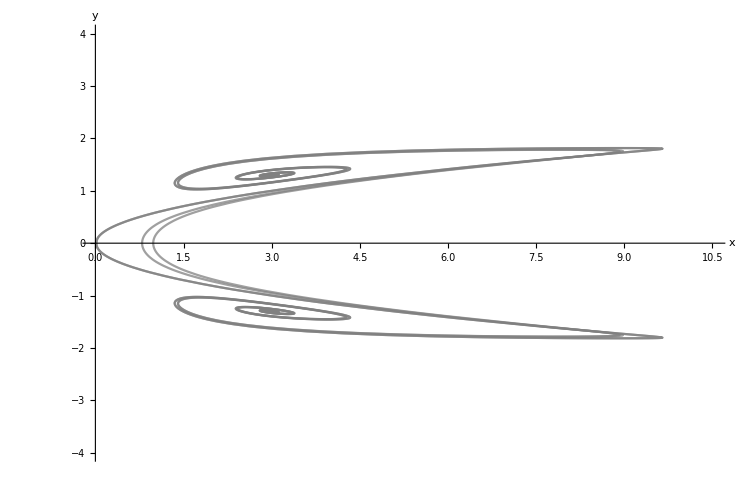

```mathematica
ParametricPlot[Evaluate[Table[{x1[t],y1[t]}/.sol[i],{i,1,6}], {t,-50,50},PlotStyle -> {{Gray, Opacity[0.75]}},PlotRange->{{0,10.5},{-4,4}}],AxesLabel->{"x","y"}]
```

InterpolatingFunction::dmval: Input value {-49.998} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

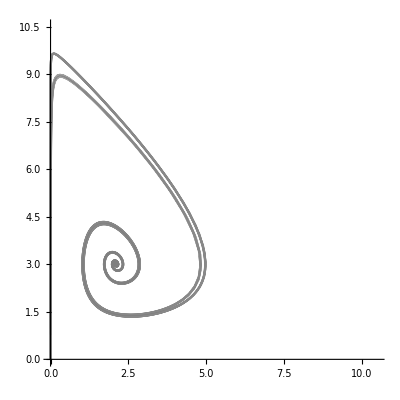

```mathematica
ParametricPlot[Evaluate[Table[{z1[t],x1[t]}/.sol[i],{i,1,6}], {t,-50,50},PlotStyle -> {{Gray, Opacity[0.75]}},PlotRange->{{0,10.5},{0,10.5}}]]
```

## Compactification

### Compact x - z Phase Space

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
deX:=X'=-3*X*(1-X)*(1+wx+ϵ*(X/(1-X)))-q*X*(1-X)*Z/(1-Z)
deZ:=Z'=-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deX==0,deZ==0},{X,Z}]
```

{{X→3/(3+q),Z→-(3 (q+q wx+3 ϵ))/(-3 q+q^2-3 q wx-9 ϵ)},{X→0,Z→0},{X→(1+wx)/(1+wx-ϵ),Z→0}}

```mathematica
FP[1]={X/.FPs[[1,1]],Z/.FPs[[1,2]]};
FP[2]={X/.FPs[[2,1]],Z/.FPs[[2,2]]};
FP[3]={X/.FPs[[3,1]],Z/.FPs[[3,2]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deX,X],D[deX,Z]}, {D[deZ,X],D[deZ,Z]}}];
J//MatrixForm
```

((3+3 wx (-1+2 X) (-1+Z)-3 Z+q Z-2 X (3-3 ϵ+Z (-3+q+3 ϵ)))/(-1+Z) | (q (-1+X) X)/(-1+Z)^2
-(q (-1+Z) Z)/(-1+X)^2 | ((-3+(3+q) X) (-1+2 Z))/(-1+X))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{X->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{X->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{X->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
(*Extra fixed points from compactification at {X = 1, Z = 0},{X = 1, Z = 1},{X = 0, Z = 1}*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(3/(3+q)
-(3 (q+q wx+3 ϵ))/(-3 q+q^2-3 q wx-9 ϵ)) | (-(9 ϵ)/q | -(3 (q^2-3 q (1+wx)-9 ϵ)^2)/(q^2 (3+q)^2)
-(3 q (3+q)^2 (q+q wx+3 ϵ))/((q^2-3 q (1+wx)-9 ϵ)^2) | 0) | ((3 (-243 q^3 ϵ+54 q^5 ϵ-3 q^7 ϵ-486 q^3 wx ϵ-162 q^4 wx ϵ+54 q^5 wx ϵ+18 q^6 wx ϵ-243 q^3 wx^2 ϵ-162 q^4 wx^2 ϵ-27 q^5 wx^2 ϵ-1458 q^2 ϵ^2-486 q^3 ϵ^2+162 q^4 ϵ^2+54 q^5 ϵ^2-1458 q^2 wx ϵ^2-972 q^3 wx ϵ^2-162 q^4 wx ϵ^2-2187 q ϵ^3-1458 q^2 ϵ^3-243 q^3 ϵ^3-q (3+q)^2 (-3 q+q^2-3 q wx-9 ϵ)^2 √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)))/(2 q^2 (3+q)^2 (-3 q+q^2-3 q wx-9 ϵ)^2)
(3 (-243 q^3 ϵ+54 q^5 ϵ-3 q^7 ϵ-486 q^3 wx ϵ-162 q^4 wx ϵ+54 q^5 wx ϵ+18 q^6 wx ϵ-243 q^3 wx^2 ϵ-162 q^4 wx^2 ϵ-27 q^5 wx^2 ϵ-1458 q^2 ϵ^2-486 q^3 ϵ^2+162 q^4 ϵ^2+54 q^5 ϵ^2-1458 q^2 wx ϵ^2-972 q^3 wx ϵ^2-162 q^4 wx ϵ^2-2187 q ϵ^3-1458 q^2 ϵ^3-243 q^3 ϵ^3+q (3+q)^2 (-3 q+q^2-3 q wx-9 ϵ)^2 √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)))/(2 q^2 (3+q)^2 (-3 q+q^2-3 q wx-9 ϵ)^2)) | (-(-27 q^2 ϵ+18 q^3 ϵ-3 q^4 ϵ-54 q^2 wx ϵ+18 q^3 wx ϵ-27 q^2 wx^2 ϵ-162 q ϵ^2+54 q^2 ϵ^2-162 q wx ϵ^2-243 ϵ^3-9 q^2 √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)+6 q^3 √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)-q^4 √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)-18 q^2 wx √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)+6 q^3 wx √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)-9 q^2 wx^2 √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)-54 q ϵ √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)+18 q^2 ϵ √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)-54 q wx ϵ √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)-81 ϵ^2 √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2))/(2 (3 q+q^2)^2 (q+q wx+3 ϵ)) | 1
-(-27 q^2 ϵ+18 q^3 ϵ-3 q^4 ϵ-54 q^2 wx ϵ+18 q^3 wx ϵ-27 q^2 wx^2 ϵ-162 q ϵ^2+54 q^2 ϵ^2-162 q wx ϵ^2-243 ϵ^3+9 q^2 √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)-6 q^3 √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)+q^4 √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)+18 q^2 wx √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)-6 q^3 wx √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)+9 q^2 wx^2 √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)+54 q ϵ √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)-18 q^2 ϵ √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)+54 q wx ϵ √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)+81 ϵ^2 √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2))/(2 (3 q+q^2)^2 (q+q wx+3 ϵ)) | 1)
(0
0) | (-3 (1+wx) | 0
0 | -3) | (-3
3 (-1-wx)) | (0 | 1
1 | 0)
((1+wx)/(1+wx-ϵ)
0) | (3 (1+wx) | (q (1+wx) ϵ)/(1+wx-ϵ)^2
0 | -3-(q (1+wx))/ϵ) | (3 (1+wx)
-(q+q wx+3 ϵ)/ϵ) | (1 | 0
-(q (1+wx) ϵ^2)/((1+wx-ϵ)^2 (q+q wx+6 ϵ+3 wx ϵ)) | 1)

```mathematica
(*Find condition for first fixed point to be complex*)
wxCond=Solve[4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2==0,{q,ϵ,wx}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{wx→-(2 q+3 ϵ)^2/(4 q^2)},{q→0,ϵ→0}}

```mathematica
wxCondition=wx/.wxCond[[1]]
```

-(2 q+3 ϵ)^2/(4 q^2)

```mathematica
(*Maximum value wx can be for positive q and negative ϵ to reproduce Fig. 9b*)
wxMax=wxCondition/.{ϵ->-0.25,q->1}
```

-0.390625

```mathematica
(*Define the differential equations in terms of their variables*)
DE[wx_,q_,ϵ_]=deX;
DM[q_]=deZ;
```

```mathematica
StreamPlot[{DE[wx,q,ϵ],DM[q]},{X,0,1},{Z,0,1},FrameLabel->{"x","Z"}]
```

### Compact x - y - z Phase Space

```mathematica
(*Define the dynamical system for compact interacting dark matter (Z) and dark energy (X)*)
```

```mathematica
deX:=X'=-3*(Y/((1-Y^2)^(1/2)))*X*(1-X)*(1+wx+ϵ*(X/(1-X)))-q*X*(1-X)*(Z/(1-Z))*(Y/((1-Y^2)^(1/2)))
deY:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((X/(1-X))+(Z/(1-Z))+3*wx*(X/(1-X))+3*ϵ*(X^2/((1-X)^2)))
deZ:=Z'=-3*Z*(1-Z)*(Y/((1-Y^2)^(1/2))) + q*(X/(1-X))*Z*(1-Z)*(Y/((1-Y^2)^(1/2)))
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deX==0,deY==0,deZ==0},{X,Y,Z}];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={X,Y/.FPs[[1,1]],Z/.FPs[[1,2]]};
FP[2]={X/.FPs[[2,1]],Y/.FPs[[2,2]],Z/.FPs[[2,3]]};
FP[3]={X/.FPs[[3,1]],Y/.FPs[[3,2]],Z/.FPs[[3,3]]};
FP[4]={X/.FPs[[4,1]],Y/.FPs[[4,2]],Z/.FPs[[4,3]]};
FP[5]={X/.FPs[[5,1]],Y/.FPs[[5,2]],Z/.FPs[[5,3]]};
FP[6]={X/.FPs[[6,1]],Y/.FPs[[6,2]],Z/.FPs[[6,3]]};
FP[7]={X/.FPs[[7,1]],Y/.FPs[[7,2]],Z/.FPs[[7,3]]};
FP[8]={X/.FPs[[8,1]],Y/.FPs[[8,2]],Z/.FPs[[8,3]]};
FP[9]={X/.FPs[[9,1]],Y/.FPs[[9,2]],Z/.FPs[[9,3]]};
FP[10]={X/.FPs[[10,1]],Y/.FPs[[10,2]],Z/.FPs[[10,3]]};
```

```mathematica
(*Put fixed points into a table*)
(*FPs=Table[FP[i],{i,11,18}];*)
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deX,X],D[deX,Y],D[deX,Z]}, {D[deY,X],D[deY,Y],D[deY,Z]},{D[deZ,X],D[deZ,Y],D[deZ,Z]}}];
J//MatrixForm
```

((Y (3+3 wx (-1+2 X) (-1+Z)-3 Z+q Z-2 X (3-3 ϵ+Z (-3+q+3 ϵ))))/(√(1-Y^2) (-1+Z)) | (X (3+3 wx (-1+X) (-1+Z)-3 Z+q Z-X (3-3 ϵ+Z (-3+q+3 ϵ))))/((1-Y^2)^(3/2) (-1+Z)) | (q (-1+X) X Y)/(√(1-Y^2) (-1+Z)^2)
-((1-Y^2)^(3/2) (-1+3 wx (-1+X)+X-6 X ϵ))/(6 (-1+X)^3) | (Y (2 Y^2+4 (-1+Y^2)+(1-Y^2) ((X+3 wx X)/(1-X)+Z/(1-Z)+(3 X^2 ϵ)/(-1+X)^2)))/(2 √(1-Y^2)) | -((1-Y^2)^(3/2))/(6 (-1+Z)^2)
-(q Y (-1+Z) Z)/((-1+X)^2 √(1-Y^2)) | ((-3+(3+q) X) (-1+Z) Z)/((-1+X) (1-Y^2)^(3/2)) | ((-3+(3+q) X) Y (-1+2 Z))/((-1+X) √(1-Y^2)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
(*FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm},{i,1,10}];*)
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
(*FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]*)
```

```mathematica
EqX[q_,wx_,ϵ_]=deX;
EqY[wx_,ϵ_]=deY;
EqZ[q_]=deZ;
```

```mathematica
StreamPlot3D[{EqX[q,wx,ϵ],EqY[wx,ϵ],EqZ[q]},{X,0,1},{Y,-1,1},{Z,0,1},AxesLabel->{"X","Y","Z"},StreamMarkers->"Arrow"]
```